```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy452-basicstatmech"]

fs=Style[#,FontSize->14]&;
```

/Users/pjoot/project/figures/phy452-basicstatmech

```mathematica
gThreeHalves[z_] = (4/Sqrt[Pi]) Integrate[ x^2/(E^(x^2)/z - 1), {x, 0, Infinity}]
```

PolyLog[3/2,z]

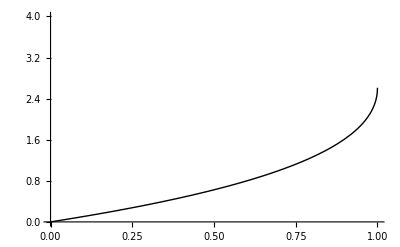

```mathematica
lecture19f32Fig1 =Plot[ gThreeHalves[z], {z,0,1}, 
PlotStyle-> {Thick, Black},
AxesLabel->{
(*"z"//fs, "g_(3/2)(z)" //fs*)
MaTeX["z"],
MaTeX["g_{3/2}(z)"]
},
PlotRange -> {Automatic, {0,4}}
]
```

```mathematica
peeters`exportForLatex["lecture19f32Fig1",lecture19f32Fig1]
```

{lecture19f32Fig1.eps,lecture19f32Fig1pn.png}